```mathematica
function1[a_,b_,g_]:=
(
i=1;
While[p[[i]] < 0.999999999999999,
AppendTo[p,f[p[[i]]]];
i++
];
i;
p;

exactPrint={};
For[m=1,m≤i,m++,
AppendTo[exactPrint,{p[[m]],f[p[[m]]]}]
];

equalPr={};
For[m=2,m≤i,m++,
AppendTo[equalPr,{p[[m]],p[[m]]}]
];

Show[Plot[f[x],{x,0,1},PlotRange->All,PlotStyle->Blue],ListPlot[{{1,f[1]},{0,f[0]}
},PlotStyle->Red],Plot[y=x,{x,0,1},PlotStyle->Gray],ListPlot[exactPrint,PlotRange->All,PlotStyle->Black],ListPlot[equalPr,PlotRange->All,PlotStyle->Black]]
)

function2[a_,b_,g_]:=(
i=1;
While[p[[i]]> 0.0001,
AppendTo[p,f[p[[i]]]];
i++
];
i;
p;

exactPrint={};
For[m=1,m≤i,m++,
AppendTo[exactPrint,{p[[m]],f[p[[m]]]}]
];

equalPr={};
For[m=2,m≤i,m++,
AppendTo[equalPr,{p[[m]],p[[m]]}]
];

Show[Plot[f[x],{x,0,1},PlotRange->All,PlotStyle->Blue],ListPlot[{{1,f[1]},{0,f[0]}
},PlotStyle->Red],Plot[y=x,{x,0,1},PlotStyle->Gray],ListPlot[exactPrint,PlotRange->All,PlotStyle->Black],ListPlot[equalPr,PlotRange->All,PlotStyle->Black]]
)

function3[a_,b_,g_]:=(
i=1;
While[p[[i]]≠ pCenter,
AppendTo[p,f[p[[i]]]];
i++
];
i;
p;

exactPrint={};
For[m=1,m≤i,m++,
AppendTo[exactPrint,{p[[m]],f[p[[m]]]}]
];

equalPr={};
For[m=2,m≤i,m++,
AppendTo[equalPr,{p[[m]],p[[m]]}]
];

Show[Plot[f[x],{x,0,1},PlotRange->All,PlotStyle->Blue],ListPlot[{{1,f[1]},{0,f[0]},{pCenter,f[pCenter]}
},PlotStyle->Red],Plot[y=x,{x,0,1},PlotStyle->Gray],ListPlot[exactPrint,PlotRange->All,PlotStyle->Black],ListPlot[equalPr,PlotRange->All,PlotStyle->Black]]
)

function4[a_,b_,g_]:=(
If[p[[1]]> pCenter, 
i=1;
While[p[[i]] <0.99999999999999,
AppendTo[p,f[p[[i]]]];
i++
];
i;
p;,

i=1;
While[p[[i]] > 0.000000001,
AppendTo[p,f[p[[i]]]];
i++
];
i;
p;
];

exactPrint={};
For[m=1,m≤i,m++,
AppendTo[exactPrint,{p[[m]],f[p[[m]]]}]
];

equalPr={};
For[m=2,m≤i,m++,
AppendTo[equalPr,{p[[m]],p[[m]]}]
];

Show[Plot[f[x],{x,0,1},PlotRange->All,PlotStyle->Blue],ListPlot[{{1,f[1]},{0,f[0]},{pCenter,f[pCenter]}
},PlotStyle->Red],Plot[y=x,{x,0,1},PlotStyle->Gray],ListPlot[exactPrint,PlotRange->All,PlotStyle->Black],ListPlot[equalPr,PlotRange->All,PlotStyle->Black]]
)

biology[a_,b_,g_]:=
(
f[x_]:= ((a-b)x^2+b*x)/((a-2b+g)x^2+2(b-g)x+g);
pCenter=(g-b)/(a-2b+g);
p={};
AppendTo[p,RandomReal[]];

If[a>b>g, function1[a,b,g],
If[a<b<g,function2[a,b,g],
If[b>g>a || b>a>g,function3[a,b,g],
If[b<g<a || b<a<g,function4[a,b,g]
]
]
]
]
)
```

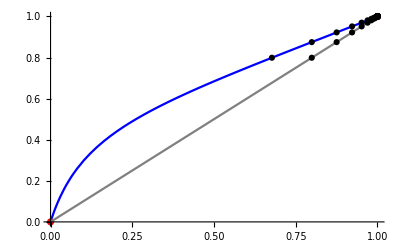

```mathematica
biology[0.8,0.5,0.1]
```

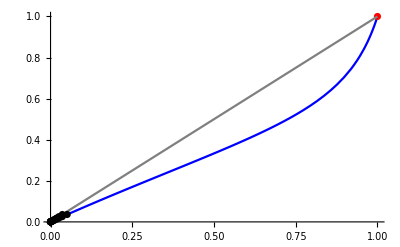

```mathematica
biology[0.1,0.5,0.7]
```

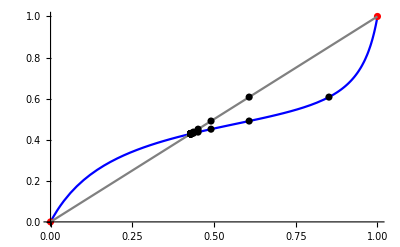

```mathematica
biology[0.1,0.9,0.3]
```

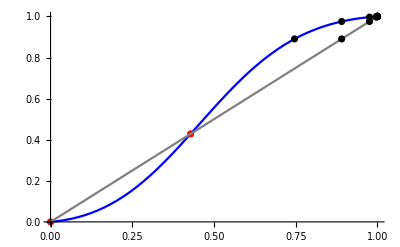

```mathematica
biology[0.9,0.1,0.7]
```